# Kansas interpolation approach in 1D To solve elliptic PDEs

## Source Function

Original function

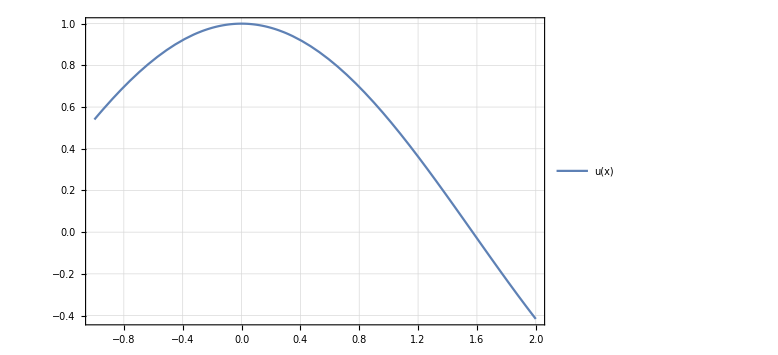

```mathematica
u[x_]=Cos[x];
f[x_]=Laplacian[u[x],{x}];
li=0;(* Inferior limit *)
ls=1;(* Superior limit*)
Print[Style["Original function",25,Blue]]
Plot[u[x],{x,li-1,ls+1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
```

## Input data

```mathematica
dx=0.01;(* Width of mesh *)
data=Range[li,ls,dx];
ndata=Dimensions[data][[1]];
```

## Computing laplacian of RBF

```mathematica
ϵ=1.0;
r[x_]=Sqrt[x^2];
ϕ[x_]=Exp[-(ϵ r[x])^2]
Lϕ[x_]=Laplacian[ϕ[x],{x}]
```

ⅇ^(-1. x^2)

-2. ⅇ^(-1. x^2)+4. ⅇ^(-1. x^2) x^2

## Building interpolation matrix A

```mathematica
(* Generating interpolation matrix A *)
A=RandomReal[{0,1},{ndata,ndata}];
For[i=1,i≤ndata,i++,
For[j=1,j≤ndata,j++,
δ=r[data[[i]]-data[[j]]];
If[i==1|| i==ndata,A[[i,j]]=ϕ[δ],
A[[i,j]]=Lϕ[δ]
]
]
]
```

## Some characteristics of A

Condition number, determinant and matrix plot

2.22574×10^19

-3.85305118604782×10^-1371

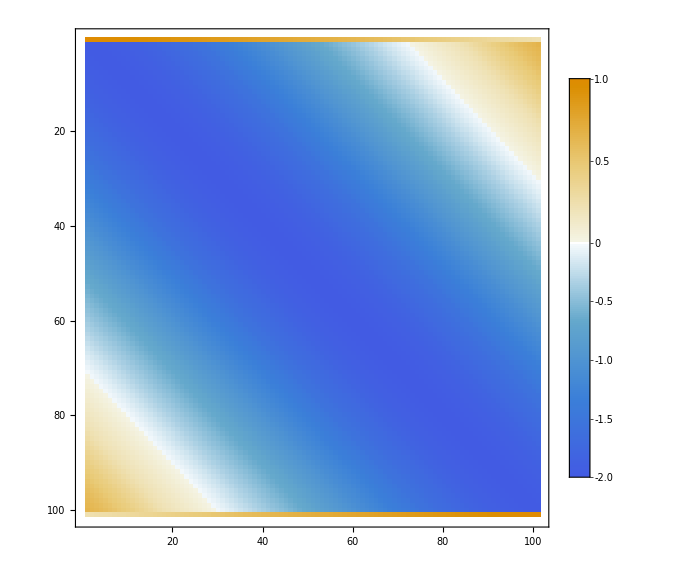

```mathematica
(* Matrix Information *)
Print[Style["Condition number, determinant and matrix plot",25,Blue]]
LinearAlgebra`MatrixConditionNumber[A,Norm->Infinity]
Det[A]
MatrixPlot[A,PlotTheme->"Detailed",ImageSize->Large]
```

## Building v: Ac=v

```mathematica
(* Building v:  A.c=v *)
v={};
For[i=1,i≤ndata,i++,
If[i==1,AppendTo[v,u[li]],
If[i==ndata,AppendTo[v,u[ls]],
AppendTo[v,f[data[[i]]]]
]
]
]
```

## Solving the linear system

```mathematica
(* Solve the system *)
c=LinearSolve[A,v];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 0.9999, 0.9996, 0.9991, 0.998401, 0.997503, 0.996406, 0.995112, 0.99362, 0.991933, 0.99005, 0.987973, 0.985703, « 25 », 0.865541, 0.858902, 0.852144, 0.845269, 0.838283, 0.831187, 0.823987, 0.816686, 0.809288, 0.801797, 0.794216, 0.786549, « 51 »}, « 49 », « 51 »} may contain significant numerical errors.

## Building the interpolation function

```mathematica
(* Building interpolation function Pf *)
P=0;
For[i=1,i≤ndata,i++,
ξ=data[[i]];
P+=c[[i]]ϕ[x-ξ]
]
Pf[x_]=P;
Error[x_]=Pf[x]-u[x];
```

## Final Results

Interpolation function and Error function

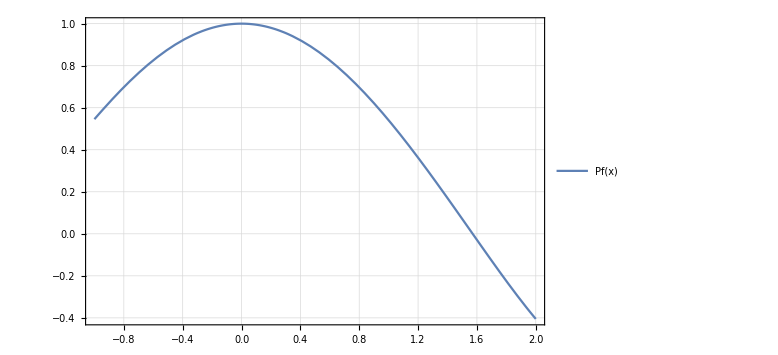

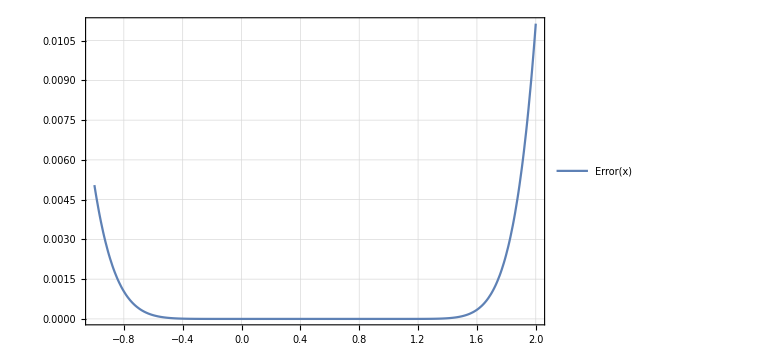

RMS error

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.97829×10^-15 and 1.7197×10^-15 for the integral and error estimates.

6.97829×10^-15

```mathematica
Print[Style["Interpolation function and Error function",25,Blue]]
Plot[Pf[x],{x,li-1,ls+1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
Plot[Error[x],{x,li-1,ls+1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]

(* RMS error *)
Print[Style["RMS error",25,Blue]]
NIntegrate[(Error[x])^2,{x,0,1},{y,0,1}]
```